```mathematica
Needs["ErrorBarPlots`"];
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

# Pd DCA vary T

## tpd=1.13,tpp=0.49,Udd=8.5,Upp=0

## beta=8, L=4*4

```mathematica
dcan4by4b8Upp0={0.7,0.75,0.8,0.85,0.9,0.95,1,1.05,1.1 ,1.15,1.2,1.25,1.3};
```

```mathematica
dcapd4by4b8Upp0={3.046467752230849,2.995008809900182,2.9033565828822545,2.768166691006621,2.5924815630778015,2.3542615318538758,2.1295426999895954,2.1414662867324674,2.2466935221865456,2.3700387055843226,2.4756003451959443,2.570485503644828,2.6473149209143343};
```

```mathematica
dcapderr4by4b8Upp0={0,0,0,0,0,0,0,0,0,0,0,0,0};
```

```mathematica
dcapdvsn4by4b8Upp0=Table[{dcan4by4b8Upp0[[i]],dcapd4by4b8Upp0[[i]]},{i,1,13}];
```

## beta=16, L=4*4

```mathematica
dcan4by4b16Upp0={0.7,0.75,0.8,0.85,0.9,0.95,1,1.05,1.1 ,1.15,1.2,1.25,1.3};
```

```mathematica
dcapd4by4b16Upp0={3.6593351039077255,3.757433157945449,3.80914175450281,3.7535841096157108,3.6079832514210213,3.2302206770740143,2.5091847896786073,2.5156772154267495,2.811265295220425,3.0614042590743566,3.2270977603747517,3.3279197706655173,3.3771679198433677};
```

```mathematica
dcapderr4by4b16Upp0={0,0,0,0,0,0,0,0,0,0,0,0,0};
```

```mathematica
dcapdvsn4by4b16Upp0=Table[{dcan4by4b16Upp0[[i]],dcapd4by4b16Upp0[[i]]},{i,1,13}];
```

## beta=24, L=4*4

```mathematica
dcan4by4b24Upp0={0.7,0.75,0.8,0.85,0.9,0.95,1,1.05,1.1 ,1.15,1.2,1.25,1.3};
```

```mathematica
dcapd4by4b24Upp0={3.8085172117802637,3.994136049499172,4.2564764336772845,4.481763498949158,4.408216614864361,3.918714440111815,2.3761649455880143,2.603088585967762,3.142313213801558,3.564251386926816,3.818757480322584,3.9014650404822335,3.855340880253866};
```

```mathematica
dcapderr4by4b24Upp0={0,0,0,0,0,0,0,0,0,0,0,0,0};
```

```mathematica
dcapdvsn4by4b24Upp0=Table[{dcan4by4b24Upp0[[i]],dcapd4by4b24Upp0[[i]]},{i,1,13}];
```

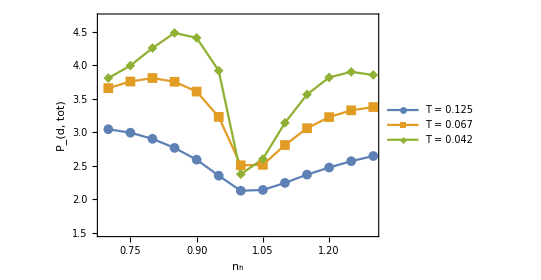

```mathematica
dcapdvsn4by4varybeta=ListPlot[{dcapdvsn4by4b8Upp0,dcapdvsn4by4b16Upp0,dcapdvsn4by4b24Upp0},PlotMarkers->{Automatic,10},PlotRange->{Automatic,{1.51,4.7}},PlotLegends->Placed[LineLegend[{"T = 0.125","T = 0.067","T = 0.042"},LabelStyle->{14},LegendLayout->{"Row",1}],{0.5,0.1}],Frame->True,AspectRatio->0.7,BaseStyle->{FontSize->18,FontFamily->"times New Roman"},FrameLabel->{"n_h","P_(d, tot)"},FrameLabel->{"n","P_d","L=4*4"},Joined->True]
```

```mathematica
dcapdvsn4by4varybeta=Show[dcapdvsn4by4varybeta(*,Graphics[Text[Style["(a)",FontSize->18,Black],{1.25,0.6}]]*)];
```

```mathematica
Export["/Users/cosdis/Desktop/threeband_project/MS_pairing_correlation/dcapdvsn4by4varybeta.pdf",dcapdvsn4by4varybeta,"PDF"];
```

# λd DCA vary T

## tpd=1.13,tpp=0.49,Udd=8.5,Upp=0

## beta=8, L=4*4

```mathematica
dcan4by4b8Upp0={0.7,0.75,0.8,0.85,0.9,0.95,1,1.05,1.1 ,1.15,1.2,1.25,1.3};
```

```mathematica
dcalambdad4by4b8Upp0={0.045991458,0.069737606,0.098049539,0.138440026,0.193914399,0.263,0.328941495,0.283204454,0.208766482,0.136144375,0.080141936,0.042964316,0.023102747};
```

```mathematica
dcapd04by4b8Upp0={0.33712838958745556,0.5027773965221463,0.5411418944830925,0.597476253758294,0.5400044570542011,0.4371405262728784,0.3120110391824297,0.2744415504875778,0.2920787744955356,0.3041748269368877,0.2909094170846184,0.19085596925335335,0.05263758001098535};
```

```mathematica
dcalambdadvsn4by4b8Upp0=Table[{dcan4by4b8Upp0[[i]],dcalambdad4by4b8Upp0[[i]]},{i,1,13}];
```

```mathematica
Pd04by4b8vsdensity=Table[{dcan4by4b8Upp0[[i]],dcapd04by4b8Upp0[[i]]},{i,1,13}];
```

```mathematica
dcapdseptot4by4b8Upp0=Table[dcapd04by4b8Upp0[[i]]/(1-dcalambdad4by4b8Upp0[[i]]),{i,1,Length[dcan4by4b8Upp0]}];
```

```mathematica
dcapdseptotvsn4by4b8Upp0=Table[{dcan4by4b8Upp0[[i]],dcapdseptot4by4b8Upp0[[i]]},{i,1,13}];
```

## beta=16, L=4*4

```mathematica
dcan4by4b16Upp0={0.7,0.75,0.8,0.85,0.9,0.95,1,1.05,1.1 ,1.15,1.2,1.25,1.3};
```

```mathematica
dcalambdad4by4b16Upp0={0.068802793 ,0.103740849 ,0.151425126 ,0.215637531 ,0.329753062 ,0.481274795 ,0.665127312 ,0.643191096 ,0.477346313 ,0.323446879 ,0.19367345 ,0.107570814 ,0.051533715};
```

```mathematica
dcapd04by4b16Upp0={0.29331726100866085,0.3690265650881975,0.44885795328695505,0.6102052505350688,0.9402319651459166,0.9386668276233228,0.4266987696427761,0.38501127755694253,0.6165596936846296,0.7855356903529345,0.7947974768141328,0.7300178380843022,0.47415262599060937};
```

```mathematica
dcalambdadvsn4by4b16Upp0=Table[{dcan4by4b16Upp0[[i]],dcalambdad4by4b16Upp0[[i]]},{i,1,13}];
```

```mathematica
Pd04by4b16vsdensity=Table[{dcan4by4b16Upp0[[i]],dcapd04by4b16Upp0[[i]]},{i,1,13}];
```

```mathematica
dcapdseptot4by4b16Upp0=Table[dcapd04by4b16Upp0[[i]]/(1-dcalambdad4by4b16Upp0[[i]]),{i,1,Length[dcan4by4b16Upp0]}];
```

```mathematica
dcapdseptotvsn4by4b16Upp0=Table[{dcan4by4b16Upp0[[i]],dcapdseptot4by4b16Upp0[[i]]},{i,1,13}];
```

## beta=24, L=4*4

```mathematica
dcan4by4b24Upp0={0.7,0.75,0.8,0.85,0.9,0.95,1,1.05,1.1 ,1.15,1.2,1.25,1.3};
```

```mathematica
dcalambdad4by4b24Upp0={0.08072679,0.119072624,0.19064835,0.318642933,0.420291611,0.605539088,0.821419166,0.831045983,0.690624383,0.5540757,0.306966757,0.163499091,0.081250164};
```

```mathematica
dcalambdadvsn4by4b24Upp0=Table[{dcan4by4b24Upp0[[i]],dcalambdad4by4b24Upp0[[i]]},{i,1,13}];
```

```mathematica
dcalambdadvsn4by4b24Upp0=Table[{dcan4by4b24Upp0[[i]],dcalambdad4by4b24Upp0[[i]]},{i,1,13}];
```

```mathematica
dcapd04by4b24Upp0={0.1761664281103336,0.7626271493740573,0.3964931459264169,0.6047800470677297,0.5801902677542905,0.6541392336199892,0.2811719608570539,0.2630461715117695,0.6264640541896183,0.8959720420705696,0.7740189381771925,0.6509064874355834,0.3714947672569387};
```

```mathematica
Pd04by4b24vsdensity=Table[{dcan4by4b24Upp0[[i]],dcapd04by4b24Upp0[[i]]},{i,1,13}];
```

```mathematica
dcalambdadvsn4by4varybeta0=ListPlot[{dcalambdadvsn4by4b8Upp0,dcalambdadvsn4by4b16Upp0,dcalambdadvsn4by4b24Upp0},PlotMarkers->{Automatic,10},(*PlotLegends->Placed[LineLegend[{"β=8","β=16","β=24"},LabelStyle->{14},LegendLayout->{"Row",4}],{0.15,0.7}],*)Frame->True,AspectRatio->0.7,BaseStyle->{FontSize->18,FontFamily->"times New Roman"},FrameLabel->{"n_h","λ_d","L=4*4"},Joined->True];
```

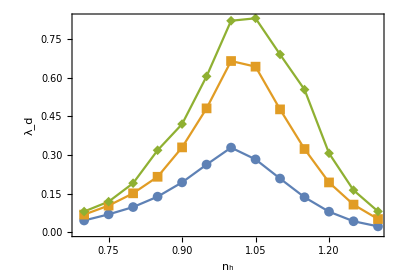

```mathematica
dcalambdadvsn4by4varybeta=Show[dcalambdadvsn4by4varybeta0(*,Graphics[Text[Style["(b)",FontSize->18,Black],{1.25,0.81}]]*)]
```

```mathematica
dcaldpd4by4b8Upp0=Table[{dcan4by4b24Upp0[[i]],1/(1-dcalambdad4by4b8Upp0[[i]])},{i,1,Length[dcalambdad4by4b8Upp0]}];
```

```mathematica
dcaldpd4by4b16Upp0=Table[{dcan4by4b24Upp0[[i]],1/(1-dcalambdad4by4b16Upp0[[i]])},{i,1,Length[dcalambdad4by4b16Upp0]}];
```

```mathematica
dcaldpd4by4b24Upp0=Table[{dcan4by4b24Upp0[[i]],1/(1-dcalambdad4by4b24Upp0[[i]])},{i,1,Length[dcalambdad4by4b24Upp0]}];
```

```mathematica
dcaldpdvsn4by4varybeta0=ListPlot[{dcaldpd4by4b8Upp0,dcaldpd4by4b16Upp0,dcaldpd4by4b24Upp0},PlotMarkers->{Automatic,10}(*PlotLegends->Placed[LineLegend[{"β=8","β=16","β=24"},LabelStyle->{14},LegendLayout->{"Row",4}],{0.15,0.7}]*),Frame->True,AspectRatio->0.7,BaseStyle->{FontSize->18,FontFamily->"times New Roman"},FrameLabel->{"n_h","1/(1-λ_d)","L=4*4"},Joined->True,PlotRange->{All,{0.5,6.5}}];
```

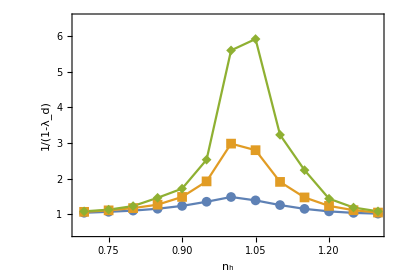

```mathematica
dcaldpdvsn4by4varybeta=Show[dcaldpdvsn4by4varybeta0(*,Graphics[Text[Style["(c)",FontSize->18,Black],{1.25,5.9}]]*)]
```

```mathematica
Export["/Users/cosdis/Desktop/threeband_project/MS_pairing_correlation/dcaldpdvsn4by4varybeta.pdf",dcaldpdvsn4by4varybeta,"PDF"];
```

```mathematica
dcapd04by4b8Upp0=Table[{dcan4by4b24Upp0[[i]],dcapd4by4b8Upp0[[i]]/dcaldpd4by4b8Upp0[[i,2]]},{i,1,Length[dcalambdad4by4b8Upp0]}];
```

```mathematica
dcapd04by4b16Upp0=Table[{dcan4by4b24Upp0[[i]],dcapd4by4b16Upp0[[i]]/dcaldpd4by4b16Upp0[[i,2]]},{i,1,Length[dcalambdad4by4b16Upp0]}];
```

```mathematica
dcapd04by4b24Upp0=Table[{dcan4by4b24Upp0[[i]],dcapd4by4b24Upp0[[i]]/dcaldpd4by4b24Upp0[[i,2]]},{i,1,Length[dcalambdad4by4b24Upp0]}];
```

```mathematica
dcapd0vsn4by4varybeta0=ListPlot[{dcapd04by4b24Upp0,dcapd04by4b16Upp0,dcapd04by4b8Upp0},PlotMarkers->{Automatic,10}(*PlotLegends->Placed[LineLegend[{"β=8","β=16","β=24"},LabelStyle->{14},LegendLayout->{"Row",4}],{0.15,0.7}]*),Frame->True,AspectRatio->0.7,BaseStyle->{FontSize->18,FontFamily->"times New Roman"},FrameLabel->{"n_h","P_(d, tot)(1-λ_d)","L=4*4"},Joined->True,PlotRange->Automatic];
```

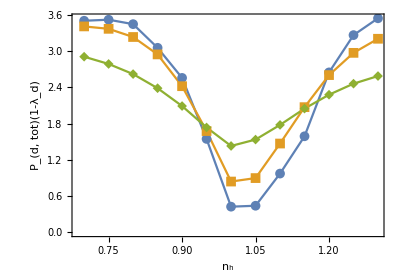

```mathematica
dcapd0vsn4by4varybeta=Show[dcapd0vsn4by4varybeta0(*,Graphics[Text[Style["(c)",FontSize->18,Black],{1.25,5.9}]]*)]
```